# Subspace recompilation for BCS Hamiltonian

Set environment, such as threads, gpu, etc.

```mathematica
SetEnvironment["OMP_NUM_THREADS"->"8"]
SetDirectory[NotebookDirectory[]];
```

Load the QuESTLink

```mathematica
Import["/home/cica/programs/QuESTlink/Link/QuESTlink.m"];
CreateLocalQuESTEnv["quest_link_cpu"];
```

### Modules

```mathematica
GetBlocks::usage="GetBlocks[blockdiagmat_,draw_:True]. Partition indices of a matrix by its blocks.";
GetBlocks[mat_,draw_:True]:=Module[{adjmat,dim=Length@mat,graph},
adjmat=ConstantArray[0,{dim,dim}];
Table[adjmat⟦i,j⟧=If[mat⟦i,j⟧==0,0,1],{i,dim},{j,dim}];
graph=AdjacencyGraph@adjmat;
If[draw,Print@graph];
ConnectedComponents@graph-1
]
```

## BCS simulation

```mathematica
(* non-iteracting harmonic oscillator-type energy levels *)
ϵ=ω(#+0.5)&/@Range[0,4];
(* time-dependent coupling function *)
coupling[t_,g0_,gc_]:=ExpandAll[
(ArcTan[(t-t1)J/(ℏ Γ)]+π/2)(ArcTan[(t2-t)J/(ℏ Γ)]+π/2)(gc-g0)/π^2+g0
]
```

```mathematica
constants={
(* time start to quench and reverse. J is an arbitrary energy unit *)
t1->9 ℏ/J,
t2->18 ℏ/J,
(* initial coupling constant*)
Γ->0.1,
(* frequency *)
ω->5J/3
};
```

```mathematica
(* mean-field eigenvalues *)
Ej[ϵ_,Δ_]:=Sqrt[ϵ^2+Abs[Δ]^2]
(* superconducting gap *)
(*2/g=∑_k 1/Subscript[E, k] tanh[Subscript[E, k]/(2 Subscript[k, b] Temp)]*)
(* since we consider temperature Temp=0, tanh(∞)=1 *)
(* Superconducting gaps*)
Δ0=J;
Δc=2J;
```

```mathematica
g0=2 /Total[1/Ej[ϵ,Δ0]];
gc=2/ Total[1/Ej[ϵ,Δc]];
```

The entire BCS Hamiltonian

```mathematica
Hgaudin[q_,n_,ϵ_,g_]:=Total@Table[({Subscript[X, q],Subscript[Y, q],Subscript[Z, q]}.{Subscript[X, j],Subscript[Y, j],Subscript[Z, j]})/(2(ϵ[[q+1]]-ϵ[[j+1]])), {j,Complement[Range[0,n-1],{q}]}]+Subscript[Z, q]/g
```

```mathematica
HBCS[n_,ϵ_,τ_]:=With[{g=coupling[τ*ℏ/Δ0,g0,gc]/.constants},
SimplifyPaulis@Chop@ExpandAll[
Total@Table[
Simplify[(-g ϵ[[q+1]]+g^2/2)Hgaudin[q,n,ϵ,g]/Δ0/.constants,J>0]
,{q,n-1}]+
SimplifyPaulis@Chop@ExpandAll[SimplifyPaulis@Simplify[g^3/(4Δ0)*(Total@Table[Hgaudin[q,n,ϵ,g],{q,0,n-1}])^2/.constants,J>0]]
]
]
```

Constants

```mathematica
(*mean field-eigenvalues*)
ej=Simplify[Ej[ϵ,Δ0]/.constants,J>0];
(* |Subscript[v, j]|^2, |Subscript[u, j]|^2 *)
ujs=Simplify[0.5(1+ϵ/ej)/.constants,J>0];
vjs=Simplify[0.5(1-ϵ/ej)/.constants,J>0];
```

```mathematica
(*  
Subscript[u, j] 0-Subscript[v, j] 1;
Ry[θ]0=Cos[θ/2]0-Sin[θ/2]1 
 *)
θinit=2*ArcCos@Sqrt@ujs;
```

initial states and memory allocation

```mathematica
DestroyAllQuregs[]
{ψmf,ψexact,ψinitmf,ψinitexact}=CreateQuregs[5,4];
```

```mathematica
(*exact groundstate*)
hbcs0=HBCS[5,ϵ,0];
{eigval,eigvec}=Eigensystem[CalcPauliStringMatrix@hbcs0];
Ordering[eigval,1];
initv=eigvec[[First@Ordering[eigval,1]]];
SetQuregMatrix[ψinitexact,initv];

(* mean field grounstate (product state) *)
ApplyCircuit[InitZeroState@ψinitmf,Table[Subscript[Ry, j-1][θinit[[j]]],{j,5}]];
```

This part (roughly)shows that in the case of exact ground state, the propagators preserves states with hamming weight 1

```mathematica
(*exact groundstate*)
hbcs0=HBCS[5,ϵ,0];
{eigval,eigvec}=Eigensystem[CalcPauliStringMatrix@hbcs0];
Ordering[eigval,1];
initv=List/@eigvec[[First@Ordering[eigval,1]]];
```

Low g(t)

```mathematica
hbcs0mat=CalcPauliStringMatrix[HBCS[5,ϵ,0]]//Chop;
hbcs0mat9=MatrixExp[-ⅈ *0.5*hbcs0mat  ]//Chop;
```

```mathematica
blocks=GetBlocks[hbcs0mat9,False]
```

{{7,11,13,14,19,21,22,25,26,28},{3,5,6,9,10,12,17,18,20,24},{15,23,27,29,30},{1,2,4,8,16},{31},{0}}

```mathematica
(*hamming-weight preserving blocks*)
Table[Length@block->{BaseForm[#,2]&/@block},{block,blocks}]//Column
```

10→{{111_2,1011_2,1101_2,1110_2,10011_2,10101_2,10110_2,11001_2,11010_2,11100_2}}
10→{{11_2,101_2,110_2,1001_2,1010_2,1100_2,10001_2,10010_2,10100_2,11000_2}}
5→{{1111_2,10111_2,11011_2,11101_2,11110_2}}
5→{{1_2,10_2,100_2,1000_2,10000_2}}
1→{{11111_2}}
1→{{0_2}}

```mathematica
CloneQureg[ψmf,ψinitmf];
CloneQureg[ψexact,ψinitexact];
ApplyCircuit[ψmf,Subscript[U, Sequence@@Range[0,4]][hbcs0mat9]];
ApplyCircuit[ψexact,Subscript[U, Sequence@@Range[0,4]][hbcs0mat9]];
```

```mathematica
(* mean-field approximate ground state is bad, and it's all over the place*)
vmf=Chop@GetQuregMatrix@ψmf;
Table[If[vmf[[j]]!=0,{BaseForm[j-1,2],1},{BaseForm[j-1,2],0}],{j,Length@vmf}]
```

{{0_2,1},{1_2,1},{10_2,1},{11_2,1},{100_2,1},{101_2,1},{110_2,1},{111_2,1},{1000_2,1},{1001_2,1},{1010_2,1},{1011_2,1},{1100_2,1},{1101_2,1},{1110_2,1},{1111_2,1},{10000_2,1},{10001_2,1},{10010_2,1},{10011_2,1},{10100_2,1},{10101_2,1},{10110_2,1},{10111_2,1},{11000_2,1},{11001_2,1},{11010_2,1},{11011_2,1},{11100_2,1},{11101_2,1},{11110_2,1},{11111_2,1}}

```mathematica
(* The exact ground state preserves hamming weight 1*)
vex=Chop@GetQuregMatrix@ψexact;
Table[If[vex[[j]]!=0,{BaseForm[j-1,2]},Sequence@@{}],{j,Length@vex}]//Column
```

{1_2}
{10_2}
{100_2}
{1000_2}
{10000_2}

High g(t)

```mathematica
hbcs10=HBCS[5,ϵ,10];
hbcs10mat=CalcPauliStringMatrix[hbcs10]//Chop;
hbcs10mat05=MatrixExp[-ⅈ hbcs10mat 0.5]//Chop;
```

```mathematica
blocks=GetBlocks[hbcs10mat05,False]
```

{{7,11,13,14,19,21,22,25,26,28},{3,5,6,9,10,12,17,18,20,24},{15,23,27,29,30},{1,2,4,8,16},{31},{0}}

```mathematica
ApplyCircuit[ψmf,Subscript[U, Sequence@@Range[0,4]][hbcs10mat05]];
ApplyCircuit[ψexact,Subscript[U, Sequence@@Range[0,4]][hbcs10mat05]];
```

```mathematica
(* Still preserving the ones at high and low g(t)*)
vex=Chop@GetQuregMatrix@ψexact;
Table[If[vex[[j]]!=0,{BaseForm[j-1,2]},Sequence@@{}],{j,Length@vex}]//Column
```

{1_2}
{10_2}
{100_2}
{1000_2}
{10000_2}

## Obtain the expression ⅇ^(-i δt H_BCS)

```mathematica
(* Low resolution *)
τs=DeleteDuplicates@Chop@Join[{0.,8.5},Range[8.5,18.5,0.2],{18.5,27}]
(* the timesteps *)
δτ=Table[τs[[i]]-τs[[i-1]],{i,2,Length@τs}];
PrependTo[δτ,0];
(*sanity check*)
And@@Table[τs[[i]]==Total[δτ[[#]]&/@Range[i]],{i,Length@τs}]
(*τ=t J/ℏ*)
```

{0,8.5,8.7,8.9,9.1,9.3,9.5,9.7,9.9,10.1,10.3,10.5,10.7,10.9,11.1,11.3,11.5,11.7,11.9,12.1,12.3,12.5,12.7,12.9,13.1,13.3,13.5,13.7,13.9,14.1,14.3,14.5,14.7,14.9,15.1,15.3,15.5,15.7,15.9,16.1,16.3,16.5,16.7,16.9,17.1,17.3,17.5,17.7,17.9,18.1,18.3,18.5,27}

True

The time-dependent gap Δ is controlled through g(t). Definition of g(t) is here

```mathematica
Length@τs
```

53

```mathematica
(*τ=t J/ℏ*)
```

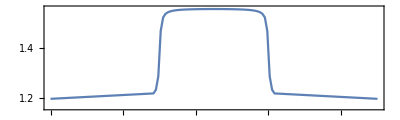

```mathematica
gvals=Simplify[(coupling[#*ℏ/Δ0,g0,gc]/Δ0&/@τs)//.constants,J>0];
ListPlot[Transpose@{τs,gvals},PlotRange->{1.16,1.56},Joined->True,AspectRatio->0.3,Frame->True,FrameTicks->{{Range[1,1.55,0.05],None},{Range[0,27,1],None}}]
```

```mathematica
δτ
```

{0,8.5,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,8.5}

Cycle 1@Tue 13 Dec 2022 01:31:39 completed with ngates=3, cost=0.34141204243610734, at eval=386

Cycle 2@Tue 13 Dec 2022 01:31:40 completed with ngates=4, cost=0.33405656674548945, at eval=672

Cycle 3@Tue 13 Dec 2022 01:31:41 completed with ngates=5, cost=0.33404835715082737, at eval=1008

Cycle 4@Tue 13 Dec 2022 01:31:42 adjust hyperparams, slowdown:True

Cycle 5@Tue 13 Dec 2022 01:31:43 adjust hyperparams, slowdown:True

pruning exceeds the maxcost: 1.×10^-9; cost=0.334048

τ=8.5; δ=8.5; cost=0.334048; ngates=5; runtime=0.0783314 min

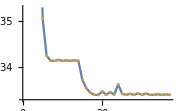

Cycle 1@Tue 13 Dec 2022 01:31:44 completed with ngates=3, cost=0.3275200567017338, at eval=327

Cycle 2@Tue 13 Dec 2022 01:31:45 completed with ngates=4, cost=0.18649582857368752, at eval=680

Cycle 3@Tue 13 Dec 2022 01:31:46 completed with ngates=7, cost=0.18646326243821, at eval=1070

Cycle 4@Tue 13 Dec 2022 01:31:47 adjust hyperparams, slowdown:True

Cycle 5@Tue 13 Dec 2022 01:31:49 completed with ngates=8, cost=0.18646307818979857, at eval=1733

Cycle 6@Tue 13 Dec 2022 01:31:50 adjust hyperparams, slowdown:True

Cycle 7@Tue 13 Dec 2022 01:31:52 completed with ngates=8, cost=0.186462923418798, at eval=2503

Cycle 8@Tue 13 Dec 2022 01:31:54 adjust hyperparams, slowdown:True

Cycle 9@Tue 13 Dec 2022 01:31:56 adjust hyperparams, slowdown:True

pruning exceeds the maxcost: 1.×10^-9; cost=0.186463

τ=8.7; δ=0.2; cost=0.186463; ngates=8; runtime=0.227845 min

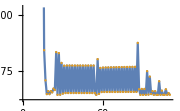

Cycle 1@Tue 13 Dec 2022 01:31:58 completed with ngates=2, cost=0.3283187437379237, at eval=284

$Aborted

```mathematica
τ=0;
results={};
Table[
hbcsmat=Chop@MatrixExp[-ⅈ *δ*CalcPauliStringMatrix[HBCS[5,ϵ,τ]]];
τ+=δ;
DestroyAllQuregs[];
conf=DefaultConfig[5,{1,2,4,8,16}];
res=CJRecompile[5,hbcsmat,conf];
AppendTo[results,{τ,res}];
{time,Ecur,Elist,ansatz,θvars,finmsg,ncycle,fev,aborted,cycleres,elimmerge,elimbfsmall,elimmetov,elimbf}=res;
Print["τ=",τ, "; δ=",δ,"; cost=",Ecur,"; ngates=",Length@ansatz,"; runtime=",time];
Print@ListPlot[{Elist,Elist},Joined->{True,False},ImageSize->Small]
,{δ,δτ[[2;;]]}];
```